```mathematica
(*points_ needs to be >= 0 to be meaningful.*)
rootsOfUnity[points_]:=Table[{Cos[2*Pi/points*iter],Sin[2*Pi/points*iter]},{iter,0,points-1,1}]//N
```

```mathematica
rootsOfUnity[5]
```

{{1.,0.},{0.309017,0.951057},{-0.809017,0.587785},{-0.809017,-0.587785},{0.309017,-0.951057}}

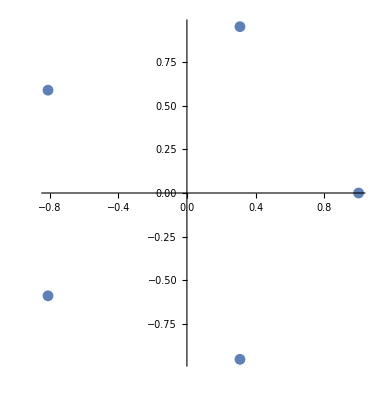

```mathematica
ListPlot[%,AspectRatio->Automatic]
```